# PSI DNP course

```mathematica
Sx=1/2{{0, 1},{1,0}};
Sy=1/2{{0,-ⅈ},{ⅈ,0}};
Sz=1/2{{1,0},{0,-1}};
II={{1,0},{0,1}};
```

## ESR

```mathematica
(* The Hamiltonian *)
H=ωS Sz+ ωμ (Sx Cos[ω t]+Sy Sin[ω t]);
H//MatrixForm
```

(ωS/2 | ωμ (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω])
ωμ (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | -ωS/2)

```mathematica
(* The initial polarization *)
(* i am not sure the polarization P is good for signle spin *)
ρ = 1/2 II+P Sz;
Tr[ρ.(2Sz)]
```

P

```mathematica
(* rotating frame *)
Hr=MatrixExp[ⅈ ω t Sz].H.MatrixExp[-ⅈ ω t Sz]-ω Sz//Simplify;
Hr//MatrixForm
```

(1/2 (-ω+ωS) | ωμ/2
ωμ/2 | (ω-ωS)/2)

```mathematica
(* The density matrix in rotating frame *)
ρr=MatrixExp[ⅈ ω t Sz].ρ.MatrixExp[-ⅈ ω t Sz]
```

{{1/2+P/2,0},{0,1/2-P/2}}

```mathematica
(* The solution of density matrix is *)
ρrs=MatrixExp[-ⅈ Hr t].ρr.MatrixExp[ⅈ Hr t]//FullSimplify;
```

```mathematica
(* density Matrix in Lab frame *)
ρS=MatrixExp[-ⅈ ω t Sz].ρrs.MatrixExp[ⅈ ω t Sz]//FullSimplify;
```

```mathematica
(* The polarization *)
FullSimplify[Tr[(2Sz).ρS],-ω^2+2 ω ωS-ωS^2-ωμ^2<0]
```

(P ((ω-ωS)^2+ωμ^2 Cos[t √((ω-ωS)^2+ωμ^2)]))/((ω-ωS)^2+ωμ^2)

```mathematica
Manipulate[
Plot[((ω-ωS)^2+ωμ^2 Cos[t √((ω-ωS)^2+ωμ^2)])/((ω-ωS)^2+ωμ^2),{t,0,10},PlotRange->1],
{ωS,1},{{ω,1},0,3},{{ωμ,1},0,2}]
```

## Flip - Flop

```mathematica
(* Spin space *)
```

```mathematica
S={II,Sx,Sy,Sz};
SS={
{IIII,IISx,IISy,IISz},
{SxII,SxSx,SxSy,SxSz},
{SyII,SySx,SySy,SySz},
{SzII,SzSx,SzSy,SzSz}};
SS=Table[KroneckerProduct[S[[i]],S[[j]]],{i,1,4},{j,1,4}];
SL={Sx+ⅈ Sy,Sx-ⅈ Sy};
SSL=Table[KroneckerProduct[SL[[i]],SL[[j]]],{i,1,2},{j,1,2}];
```

```mathematica
(* Hamiltonian *)
H=ωS1 SS[[4,1]]+ωS2 SS[[1,4]]+A SSL[[1,2]]+A SSL[[2,1]];
H//MatrixForm
```

(ωS1/2+ωS2/2 | 0 | 0 | 0
0 | ωS1/2-ωS2/2 | A | 0
0 | A | -ωS1/2+ωS2/2 | 0
0 | 0 | 0 | -ωS1/2-ωS2/2)

```mathematica
(* density matrix *)
ρ = KroneckerProduct[1/2 II+P1 Sz,1/2 II+P2 Sz];
```

```mathematica
(* solution to density matrix *)
ρs=MatrixExp[-ⅈ H t].ρ.MatrixExp[ⅈ H t]//FullSimplify;
```

```mathematica
(* Polarization *)
FullSimplify[Tr[(2 SS[[4,1]]).ρs],-4 A^2-(ωS1-ωS2)^2<0]
FullSimplify[Tr[(2 SS[[1,4]]).ρs],-4 A^2-(ωS1-ωS2)^2<0]
```

(2 A^2 (P1+P2)+P1 (ωS1-ωS2)^2+2 A^2 (P1-P2) Cos[t √(4 A^2+(ωS1-ωS2)^2)])/(4 A^2+(ωS1-ωS2)^2)

(2 A^2 (P1+P2)+P2 (ωS1-ωS2)^2+2 A^2 (-P1+P2) Cos[t √(4 A^2+(ωS1-ωS2)^2)])/(4 A^2+(ωS1-ωS2)^2)

```mathematica
Manipulate[
Plot[{(2 A^2 (P1+P2)+P1 (ωS1-ωS2)^2+2 A^2 (P1-P2) Cos[t √(4 A^2+(ωS1-ωS2)^2)])/(4 A^2+(ωS1-ωS2)^2),(2 A^2 (P1+P2)+P2 (ωS1-ωS2)^2+2 A^2 (-P1+P2) Cos[t √(4 A^2+(ωS1-ωS2)^2)])/(4 A^2+(ωS1-ωS2)^2)},{t,0,10},PlotRange->1],
{P1,-1,1},{{P2,1},-1,1},{ωS1,1},{{ωS2,1},0,3},{{A,1},0,2}]
```

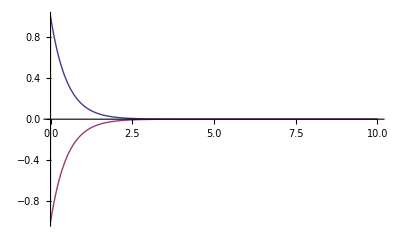

```mathematica
Plot[{Exp[- 2 t ],-Exp[- 2t]},{t,0,10},PlotRange->1]
```

## Spins System

```mathematica
(* Density Matrix *)
(* inital spin state *)
spin=Table[RandomInteger[{0,1}],{i,1,10}]
```

{0,1,0,1,1,0,0,0,1,0}

## Spin - Spin + ESR

```mathematica
(* Hamiltaina *)
H[ωS1_,ωS2_,A_,ωμ_,ω_,t_]:= ωS1 SS[[1,4]]+ ωS2 SS[[4,1]] + A SSL[[1,2]]+A SSL[[2,1]] + ωμ (SS[[1,2]]Cos[ω t]+SS[[1,3]] Sin[ω t])+ωμ (SS[[2,1]]Cos[ω t]+SS[[3,1]] Sin[ω t]);
H[ωS1,ωS2,A,ωμ,ω,t]//MatrixForm
```

(ωS1/2+ωS2/2 | ωμ (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω]) | ωμ (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω]) | 0
ωμ (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | -ωS1/2+ωS2/2 | A | ωμ (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω])
ωμ (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | A | ωS1/2-ωS2/2 | ωμ (1/2 Cos[t ω]-1/2 ⅈ Sin[t ω])
0 | ωμ (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | ωμ (1/2 Cos[t ω]+1/2 ⅈ Sin[t ω]) | -ωS1/2-ωS2/2)

```mathematica
(* Rotating frame *)
Hr[ωS1_,ωS2_,A_,ωμ_,ω_]:=MatrixExp[ⅈ ω t SS[[4,1]]].MatrixExp[ⅈ ω t SS[[1,4]]].H[ωS1,ωS2,A,ωμ,ω,t].MatrixExp[-ⅈ ω t SS[[1,4]]].MatrixExp[-ⅈ ω t SS[[4,1]]]-ω SS[[4,1]]-ω SS[[1,4]]//Simplify;
Hr[ωS1,ωS2,A,ωμ,ω]//MatrixForm
```

(1/2 (-2 ω+ωS1+ωS2) | ωμ/2 | ωμ/2 | 0
ωμ/2 | 1/2 (-ωS1+ωS2) | A | ωμ/2
ωμ/2 | A | (ωS1-ωS2)/2 | ωμ/2
0 | ωμ/2 | ωμ/2 | ω-ωS1/2-ωS2/2)

```mathematica
(* need to go to Interaction picture *)
```

```mathematica
(* density matrix *)
ρr =  KroneckerProduct[1/2 II+P1 Sz,1/2 II+P2 Sz];
```

```mathematica
ρrs=MatrixExp[-ⅈ Hr t].ρr.MatrixExp[ⅈ Hr t];
```

```mathematica
Tr[(2 SS[[4,1]]).ρrs]//FullSimplify
```

1/64 («1»)

```mathematica
PS1[P1_,P2_,ωS1_,ωS2_,A_,ωμ_,ω_,t_]:=Tr[(2 SS[[1,4]]).(MatrixExp[-ⅈ Hr[ωS1,ωS2,A,ωμ,ω] t]. KroneckerProduct[1/2 II+P1 Sz,1/2 II+P2 Sz].MatrixExp[ⅈ Hr[ωS1,ωS2,A,ωμ,ω] t])]
PS2[P1_,P2_,ωS1_,ωS2_,A_,ωμ_,ω_,t_]:=Tr[(2 SS[[4,1]]).(MatrixExp[-ⅈ Hr[ωS1,ωS2,A,ωμ,ω] t]. KroneckerProduct[1/2 II+P1 Sz,1/2 II+P2 Sz].MatrixExp[ⅈ Hr[ωS1,ωS2,A,ωμ,ω] t])]
```

```mathematica
PS1[1,P2,1,1,1,ωμ,1,t]//FullSimplify
```

$Aborted

```mathematica
Manipulate[
Plot[
{PS1[1,P2,1,ωS2,0.2,ωμ,ω,t],PS2[1,P2,1,ωS2,1,ωμ,ω,t]}
,{t,0,20},PlotRange->1],
{{P2,-1},-1,1},{{ωS2,1},0,3},{ωμ,1,2},{{ω,1},0,3}]
```

## Spin Lattices